# Pêndulo de Foucault

## Análise Completa

#### Integrantes do grupo: Felipe Tuyama Gabriel Amboss Israel Sena

## Introdução

Neste trabalho será analisado o movimento tridimensional do pêndulo de Foucault.

## Limpando todas as variáveis

Limpando as variáveis do problema.

```mathematica
Off[Remove::"rmnsm"];
Off[General::"spell1"];
Off[General::"spell"];
Off[Solve::"ifun"];
```

```mathematica
Remove["`*"];
$Line=0;
```

```mathematica
Names["`*"]
```

{}

## Análise de um Pêndulo Simples

### Breve introdução ao conceito de Pêndulo Simples:

Primeiramente, antes de mais nada, estudemos as propriedades dinâmicas e cinemáticas de um Pêndulo Simples.

Seja um pêndulo simples constituído por uma partícula, de massa m, presa a uma das extremidades de um fio inextensível, de comprimento L e massa irrelevante em face de m, e cuja outra extremidade está ligada a um ponto A fixo em relação à Terra, que consideraremos como origem do nosso sistema de coordenadas cartesianas.

Segue uma representação gráfica do problema (desprovida de significado físico por enquanto):

```mathematica
Manipulate[
Show[Graphics3D[{
Line[{{0,0,0},{0,0,-L}}],
Thick,Line[{{0,0,0},{L Sin[θ]Cos[ϕ],L  Sin[θ]Sin[ϕ],L Cos[θ]}}],
Polygon[{{-L,-L,-L},{-L,L,-L},{L,L,-L},{L,-L,-L}}],
Polygon[{{-L,-L,0},{-L,L,0},{L,L,0},{L,-L,0}}],
Arrow[BSplineCurve[{{0,0,L Cos[θ]/2},{L Sin[θ]Cos[ϕ]/2+Sign[θ-π]L/4,L  Sin[θ]Sin[ϕ]/2+Sign[θ-π]L/4,L Cos[θ]/2+Sign[θ-π]L/4},{L Sin[θ]Cos[ϕ]/2,L  Sin[θ]Sin[ϕ]/2,L Cos[θ]/2}}]],
Text[Style["θ",Italic,20],{L Sin[θ]Cos[ϕ]/4,L  Sin[θ]Sin[ϕ]/4,L Cos[θ]/2}],
Red, Sphere[{L Sin[θ]Cos[ϕ],L  Sin[θ]Sin[ϕ],L Cos[θ]},0.1],
Blue,Arrow[{{0,0,0},{0,0,-L/2}}],Blue,Arrow[{{0,0,0},{L/2,0,0}}],Arrow[{{0,0,0},{0,L/2,0}}]
 },ImageSize->600,Boxed->False,Axes->None  ],ViewPoint->{0,1,-0.2}], 
{{θ,2,"θ"},π/2,3π/2,.005(4 π),ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->False,AnimationRate->10},
{{θ,2,"θ"},π/2,3π/2,.005(4 π),Appearance->"Labeled"},
{{ϕ,1,"ϕ"},0.1,10,1,Appearance->"Labeled"},
{{L,1,"L"},0.1,10,1,Appearance->"Labeled"},
{{g,9.8,"g"},0.1,20,1,Appearance->"Labeled"}
]
```

### Equações Cinemáticas do movimento

Escrevendo as Equações Cinemáticas relativas à massa m:

r⃗ = {x[t],y[t],z[t]}  ⟹Piecewise[{{x[t]=L Sin[θ] Cos[ϕ], }, {y[t]=L Sin[θ] Sin[ϕ], }, {z[t]=L Cos[θ], }}]

‖r⃗‖ = L (Constante)

### Considerações do problema

Como trata-se de oscilações muito pequenas e o comprimento do fio é muito maior que a variação da componente z da posição da massa m, podemos utilizar a seguinte aproximação:

θ ≈ 0 , Sin[θ]≈θ, Cos[θ]≈1

### Equações Dinâmicas do movimento

Escrevendo as Equações Dinâmicas relativas à massa m:

Pela Segunda Lei de Newton:

∑F⃗=P⃗+T⃗
m a⃗=m g⃗-T (r⃗)/(‖r⃗‖)

Expandindo os termos:

x''[t](û)_x+y''[t](û)_y+z''[t](û)_z=g(û)_z-T/(m L)(x[t](û)_x+y[t](û)_y+z[t](û)_z )

Pelo método analítico vetorial, temos o sistema de Equações Diferenciais:

Piecewise[{{x''[t]=-T/(m L)x[t], }, {y''[t]=-T/(m L)y[t], }, {z''[t]=-T/(m L)z[t]+g, }}]

Mas como θ ≈ 0, temos z[t]=L Cos[θ]≈L (Constante), de modo que
Equilíbrio Vertical ⟹ z''[t]=-T/(m L)z[t]+g  ≈ -T/m+g =0
T ≈mg = P

Voltando ao sistema de Equações Diferenciais acima, temos:

Piecewise[{{x''[t]=-T/(m L)x[t], }, {y''[t]=-T/(m L)y[t], }, {z''[t]=-T/(m L)z[t]+g, }}]⟹   Piecewise[{{x''[t]=-g/Lx[t], }, {y''[t]=-g/Ly[t], }}]

O sistema de EDO’s é da forma

```mathematica
edo = {x''[t]==-g/L x[t], y''[t]==-g/L y[t]}
```

{x''[t]==-(g x[t])/L,y''[t]==-(g y[t])/L}

Consideremos, em um momento inicial, que o pêndulo seja solto de uma posição (X, Y, L), de tal modo que:

```mathematica
inic = { x[0]==X,y[0]==Y,x'[0]==0,y'[0]==0}
```

{x[0]==X,y[0]==Y,x'[0]==0,y'[0]==0}

Resolvendo o sistema de EDO’s:

```mathematica
sol=DSolve[Join[edo,inic],{x[t],y[t]},t]
```

{{x[t]→X Cos[(√g t)/(√L)],y[t]→Y Cos[(√g t)/(√L)]}}

### Resultado final: Posição da massa m em função do tempo.

O que nos leva ao resultado final:

x[t]=X Cos[√(g/L)t] ,   y[t]=Y Cos[√(g/L)t],  z[t]=√(L^2-x[t]^2-y[t]^2)≈  L
r[t] = {   X Cos[√(g/L)t] , Y Cos[√(g/L)t] , √(L^2-x[t]^2-y[t]^2)   }

Calculando o Período do Pêndulo:

√(g/L)t =2 π   (Período do Pêndulo)  ⟹   T =2 π √(L/g)
√(L^2-(X^2+Y^2)(Cos[(√g t)/(√L)])^2)

### Simulação dos resultados obtidos na seção anterior:

Finalmente, simulando os resultados obtidos utilizando o comando Manipulate:

```mathematica
Manipulate[
Show[Graphics3D[{
Line[{{0,0,0},{0,0,-L}}],
Polygon[{{-L,-L,-L},{-L,L,-L},{L,L,-L},{L,-L,-L}}],
Polygon[{{-L,-L,0},{-L,L,0},{L,L,0},{L,-L,0}}],
Thick,Line[{{0,0,0},{X Cos[(√g t)/(√L)],Y Cos[(√g t)/(√L)],-√(L^2-(X^2+Y^2)Cos[(√g t)/(√L)]^2)}}],
Red, Sphere[{X Cos[(√g t)/(√L)],Y Cos[(√g t)/(√L)],-√(L^2-(X^2+Y^2)Cos[(√g t)/(√L)]^2)},0.1],
Green, Opacity[.3],Polygon[{{-2 X,-2 Y,-L},{2X,2Y,-L},{2X,2Y,0},{-2X,-2Y,0}}]
 },ImageSize->500,Boxed->False,Axes->None,PlotLabel->Row[{"T =",NumberForm[6.28 Sqrt[L/g],{3,2}]," s"}]],ViewPoint->{0,1,-0.2}], 
{{t,0.1,"t"},0,20,.01,ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->False,AnimationRate->10},
{{t,0,"t"},0,20,.01,Appearance->"Labeled"},
{{X,0.1,"X"},0.1,L,0.1,Appearance->"Labeled"},
{{Y,0.1,"Y"},0.1,L,0.1,Appearance->"Labeled"},
{{L,1,"L"},0.1,5,0.25,Appearance->"Labeled"},
{{g,9.8,"g"},0.1,20,0.5,Appearance->"Labeled"}
]
```

## Limpando todas as variáveis

Limpando as variáveis do problema.

```mathematica
Off[Remove::"rmnsm"];
Off[General::"spell1"];
Off[General::"spell"];
Off[Solve::"ifun"];
```

```mathematica
Remove["`*"];
$Line=0;
```

```mathematica
Names["`*"]
```

{}

## Análise do Pêndulo de Foucault segundo a Questão 3

### Breve introdução ao conceito de Pêndulo de Foucault:

O pêndulo de Foucault é um pêndulo simples, cujo movimento evidencia o movimento de rotação da planeta Terra devido ao desvio de sua trajetória causada pela Força de Coriolis.

Para visualizar tal movimento, é preciso levar em conta a latitude (ou a colatitude, como será realizado neste exercício) e um plano de horizonte ou plano local onde se evidencia o movimento do plano de Foucault. Esquematizando o problema, temos:

```mathematica
Manipulate[
Show[Graphics3D[{
Thick,Black,Line[{{0,0,-1.15},{0,0,1.15}}],
Thick,Line[{{0,-1.15,0},{0,1.15,0}}],
Thick, Line[{{-1.15,0,0},{1.15,0,0}}],
Text[Style["O",Italic,20],{0, Sin[λ],Cos[λ]}],
Text[Style["Y",Italic,20],{1.25,0.25,0}],
Text[Style["X",Italic,20],{0.25,-1.25,0}],
Text[Style["Z",Italic,20],{0.25,0,-1.25}],
Text[Style["z",Italic,20],{0,1.5Sin[λ],1.5Cos[λ]}],
Text[Style["x",Italic,20],{0,Sin[λ]+0.5Cos[λ],Cos[λ]-0.5Sin[λ]}],
Text[Style["y",Italic,20],{0.5,Sin[λ],Cos[λ]}],
Red,Arrow[Tube[{{0,0,1},{0,0,1.5}}]],
Arrow[BSplineCurve[{{0.25,0,1.25},{0,0.25,1.25},{-0.25,0,1.25},{-0.25,-0.25,1.25}}]],
Text[Style["ω",Italic,20],{0,0,1.65}],
Blue,Arrow[BSplineCurve[{{0,0,0.5},{0,0.5  Sin[λ],0.5  Cos[λ]}}]],
Black,Arrow[BSplineCurve[{{0, Sin[λ],Cos[λ]},{0,1.5Sin[λ],1.5Cos[λ]}}]],
Arrow[BSplineCurve[{{0, Sin[λ],Cos[λ]},{0,Sin[λ]+0.5Cos[λ],Cos[λ]-0.5Sin[λ]}}]],
Arrow[BSplineCurve[{{0, Sin[λ],Cos[λ]},{0.5,Sin[λ],Cos[λ]}}]],
Text[Style["λ",Italic,20],{0,0.25 Sin[λ],0.25 +0.25 Cos[λ]}],
Black,ImageSize->{400,400},Arrow[Tube[{{0,0,0},{0,Sin[λ],Cos[λ]}}]],
Green,Opacity[.3],Sphere[{0,0,0}]
 },ImageSize->500,Boxed->False,Axes->None],ViewPoint->{∞,0,0}],
{{λ,0,"λ"},0,2π,.005(4 π),Appearance->"Labeled"}
]
```

### Escrevendo as Equações Cinemáticas do problema em Coordenadas Esféricas:

A posição da massa, com relação à origem do sistema de coordenadas local fixada em O, pode ser escrita como:

r⃗ = {x[t],y[t],z[t]}
x[t]=L Sin[θ [t]] Cos[ϕ [t]],
y[t]=L Sin[θ[t]] Sin[ϕ [t]],
z[t]=L-L Cos[θ[t]]

```mathematica
posic = 
{
xc[t]=L Sin[θ[t]] Cos[ϕ [t]],
yc[t]=L Sin[θ[t]] Sin[ϕ [t]],
zc[t]=L-L Cos[θ[t]]
}
```

{L Cos[ϕ[t]] Sin[θ[t]],L Sin[θ[t]] Sin[ϕ[t]],L-L Cos[θ[t]]}

### Escrevendo as Equações Dinâmicas em um Referencial Relativo:

Pela 2.aa Lei de Newton generalizada, para um movimento relativo de rotação, temos:

∑F⃗'=∑F⃗+OverVector[E_instein]+OverVector[C_oriolis]+OverVector[C_entrifuga]+OverVector[E_uler]

Considerando apenas as forças locais de interação e a força de Coriolis:

∑F⃗'=∑F⃗+OverVector[C_oriolis]

Pelo diagrama de forças atuando sobre a massa, temos:

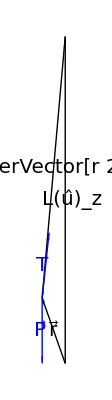

```mathematica
Graphics[{
Text[Style["r⃗",20],{-0.5,0.5}],Arrow[{{0,0},{-1,1}}],
Text[Style["OverVector[r 2]",20],{-0.7,3}],Arrow[{{0,5},{-1,1}}],
Text[Style["L(û)_z",20],{0.3,2.5}],Arrow[{{0,0},{0,5}}],
Blue,Text[Style["P⃗",20],{-1.1,0.5}],Arrow[{{-1,1},{-1,0}}],
Blue,Text[Style["T⃗",20],{-1,1.5}],Arrow[{{-1,1},{-0.7,2}}]
}]
```

m OverVector[a']=(P⃗+T⃗)+OverVector[C_oriolis]

Desenvolvendo a expressão das forças:

Piecewise[{{OverVector[a']=  ( x''[t]  (û)_x + y''[t]  (û)_y +z''[t]  (û)_z ), }, {P⃗ = -m g (û)_z, }, {T⃗ =  T OverVector[r 2]/(‖OverVector[r 2]‖)   =T(-r⃗+L(û)_z)/L, }, {OverVector[C_oriolis] = - 2 m ω⃗×OverVector[v'], }}]

m ( x''[t]  (û)_x + y''[t]  (û)_y +z''[t]  (û)_z )=-m g (û)_z + T(-r⃗+L(û)_z)/L - 2 m ω⃗×OverVector[v']

Simplificando a equação:

m( x''[t]  (û)_x + y''[t]  (û)_y +z''[t]  (û)_z) =-mg (û)_z-T/L( x [t](û)_x + y [t] (û)_y +z [t] (û)_z )+T(û)_z - 2m  ω⃗×OverVector[v']

Calculando a componente de Coriolis:

r⃗ = {x[t],y[t],z[t]}
v⃗ ={x'[t], y'[t],z'[t]}
ω⃗ = ω (Cos[λ](û)_z-Sin[λ] (û)_x )
 OverVector[a_Cor]= - 2 ω⃗×v⃗= - 2  det((û)_x | (û)_y | (û)_z
-ω Sin[λ] | 0 | ω Cos[λ]
x'[t] | y'[t] | z'[t])

```mathematica
Omega= {-ω Sin[λ] ,0,ω Cos[λ]}
```

{-ω Sin[λ],0,ω Cos[λ]}

```mathematica
aCor= -2 Simplify[Cross[Omega, {x'[t],y'[t],z'[t]}]]
```

{2 ω Cos[λ] y'[t],-2 ω (Cos[λ] x'[t]+Sin[λ] z'[t]),2 ω Sin[λ] y'[t]}

(OverVector[a_Cor])_x = 2 ω Cos[λ] y'[t]
(OverVector[a_Cor])_y = -2 ω (Cos[λ] x'[t]+Sin[λ] z'[t])
(OverVector[a_Cor])_z = 2 ω Sin[λ] y'[t]

### O Sistema de Equações Diferencias:

Substituindo a componente de Coriolis e desenvolvendo os cálculos:

x''[t]  (û)_x + y''[t]  (û)_y +z''[t]  (û)_z=-T/(m L)( x [t](û)_x + y [t] (û)_y +z [t] (û)_z )+(T/m-g)(û)_z + 2ω (  Cos[λ] y'[t](û)_x- (Cos[λ] x'[t]+Sin[λ] z'[t])(û)_y+Sin[λ] y'[t](û)_z)

Como trata-se de oscilações muito pequenas e o comprimento do fio é muito maior que a variação da componente z da posição da massa m, podemos utilizar a seguinte aproximação:

θ ≈ 0 , Sin[θ]≈θ, Cos[θ]≈1
De fato, o enunciado nos informa que:
z[t]=L-L Cos[θ[t]]≈ L-L = 0

Como consequência imediata, temos pelo equilíbrio vertical:
T/m-g≈0  ⟹ T ≈ mg

O que nos leva ao seguinte Sistema de Equações Diferenciais, pelo método analítico vetorial:

Piecewise[{{-T/(m L)x[t]+2 ω Cos[λ] y'[t]-x''[t] = 0, }, {-T/(m L)y[t]-2 ω (Cos[λ] x'[t]+Sin[λ] z'[t])-y''[t] = 0, }, {-T/mLz[t]+2 ω Sin[λ] y'[t]-z''[t] = 0, }}]

```mathematica
eq = Simplify[ {0,0,-g}-T/L   {x[t],y[t],z[t]}-{x''[t],y''[t],z''[t]}+aCor]
```

{-(T x[t])/L+2 ω Cos[λ] y'[t]-x''[t],-(T y[t])/L-2 ω (Cos[λ] x'[t]+Sin[λ] z'[t])-y''[t],-g-(T z[t])/L+2 ω Sin[λ] y'[t]-z''[t]}

Segundo a consideração do enunciado:

Piecewise[{{-g/Lx[t]+2 ω Cos[λ] y'[t]-x''[t] = 0, }, {-g/Ly[t]-2 ω (Cos[λ] x'[t]+Sin[λ] z'[t])-y''[t] = 0, }}]

Escrevendo as equações linearizadas da aceleração:

Piecewise[{{x''[t] =- g/Lx[t]+2 ω Cos[λ] y'[t], }, {y''[t] = -g/Ly[t]-2 ω Cos[λ] x'[t], }}]

Podemos resolver o sistema de EDO’s da seguinte forma:

Consideremos (x,y) como um número complexo, tal que x é a parte inteira deste número complexo e y a parte imaginária deste complexo. Assim, façamos a seguinte consideração:

Z=x[t]+y[t]ⅈ

Temos então uma única equação diferencial, dada por:

Z''[t]=-g/L Z[t] - 2ω Cos[λ] Z'[t]ⅈ
Z''[t]+ 2ω Cos[λ] Z'[t]ⅈ+g/L Z[t] =0
A fim de simplificar a notação, denotemos:
Ω = ω Cos[λ] 
w^2=g/L
Obtemos então a equação:
Z''[t]+ 2Ω Z'[t]ⅈ+w^2 Z[t] =0

Trata-se de uma EDO de segunda espécie, de modo que a sua solução geral é da forma:

Z[t]=(C[1] e^(ⅈ w t)+C[2]e^(-ⅈ w t) ) e^(-ⅈ Ω t)
Z[t]=( c1 Cos[w t]+ⅈc1 Sin[w t]+ c2 Cos[wt]-ⅈc2 Sin[wt]) (Cos[Ω  t]-ⅈSin[Ω  t])

Separando a variável complexa novamente em suas componentes, temos:

x[t]=-(c1-c2) Cos[Ω t] Sin[wt]+(c1+c2) Sin[Ω t] Cos[w t]
y[t]=(c1+c2) Cos[Ω t] Cos[w t]+(c1-c2) Sin[Ω t] Sin[w t]

Pelas condições iniciais impostas pelo enunciado, temos:

Em t=0 :{  x[0]=0, x'[0]=0, y[0]=Y, y'[0]=0  }⟹

Piecewise[{{y[0] =c1+c2 = r_0, }, {x'[0]=-(c1-c2) w+(c1+c2) Ω  =0, }}]
⟹ -(c1-c2) w+Ω  r_0=0
Piecewise[{{c1+c2 = r_0, }, {(c1-c2) =Ω/w r_0, }}]

Logo, chegamos às seguintes equações:

x[t]=r_0[- Ω/wCos[Ω t] Sin[w t]+ Sin[Ω t] Cos[w t]]
y[t]=r_0[ Cos[Ω t] Cos[w t]+Ω/w Sin[Ω t] Sin[w t]]

Substituindo as variáveis de simplificação:

x[t]=r_0[- ω Cos[λ]√(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ Sin[ω Cos[λ]t] Cos[√(g/L) t]]
y[t]=r_0[ Cos[ω Cos[λ]t ]Cos[√(g/L) t]+ω Cos[λ]√(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t]]

Mudando as equações do movimento para um referencial que também gira com a Terra:

X[t]=x[t] Cos[Ω t]-y [t]Sin[Ω t]
Y[t]=y[t] Cos[Ω t]+ x[t]Sin[Ω t]

```mathematica
Solve[{X[t]==x[t] Cos[Ω t]-y [t]Sin[Ω t], Y[t]==y[t] Cos[Ω t]+ x[t]Sin[Ω t]},{x[t],y[t]}]
```

{{x[t]→-(-Cos[t Ω] X[t]-Sin[t Ω] Y[t])/(Cos[t Ω]^2+Sin[t Ω]^2),y[t]→-(Csc[t Ω] X[t]-Cot[t Ω] Csc[t Ω] Y[t])/(1+Cot[t Ω]^2)}}

```mathematica
{{x[t]->-(-Cos[t Ω] X[t]-Sin[t Ω] Y[t])/(Cos[t Ω]^2+Sin[t Ω]^2),y[t]->-(Csc[t Ω] X[t]-Cot[t Ω] Csc[t Ω] Y[t])/(1+Cot[t Ω]^2)}}
```

{{x[t]→-(-Cos[t Ω] X[t]-Sin[t Ω] Y[t])/(Cos[t Ω]^2+Sin[t Ω]^2),y[t]→-(Csc[t Ω] X[t]-Cot[t Ω] Csc[t Ω] Y[t])/(1+Cot[t Ω]^2)}}

```mathematica
Simplify[Solve[{-(-Cos[t Ω] X[t]-Sin[t Ω] Y[t])/(Cos[t Ω]^2+Sin[t Ω]^2)==Subscript[r, 0][- Ω/w Cos[Ω t] Sin[w t]+ Sin[Ω t] Cos[w t]],
-(Csc[t Ω] X[t]-Cot[t Ω] Csc[t Ω] Y[t])/(1+Cot[t Ω]^2)==Subscript[r, 0][ Cos[Ω t] Cos[w t]+Ω/w Sin[Ω t] Sin[w t]]},{X[t],Y[t]}]]
```

{{X[t]→Cos[t Ω] r_0[-(Ω Cos[t Ω] Sin[t w])/w+Cos[t w] Sin[t Ω]]-Sin[t Ω] r_0[Cos[t w] Cos[t Ω]+(Ω Sin[t w] Sin[t Ω])/w],Y[t]→Sin[t Ω] r_0[-(Ω Cos[t Ω] Sin[t w])/w+Cos[t w] Sin[t Ω]]+Cos[t Ω] r_0[Cos[t w] Cos[t Ω]+(Ω Sin[t w] Sin[t Ω])/w]}}

Assim, obtemos a expressão:
X[t]=Cos[t Ω] r_0[-(Ω Cos[t Ω] Sin[t w])/w+Cos[t w] Sin[t Ω]]-Sin[t Ω] r_0[Cos[t w] Cos[t Ω]+(Ω Sin[t w] Sin[t Ω])/w]
Y[t]=Sin[t Ω] r_0[-(Ω Cos[t Ω] Sin[t w])/w+Cos[t w] Sin[t Ω]]+Cos[t Ω] r_0[Cos[t w] Cos[t Ω]+(Ω Sin[t w] Sin[t Ω])/w]

Simplificando-a, obtemos finalmente a Equação Geral do movimento do Pêndulo de Foucault para um observador na Terra:

X[t]=-r_0ω Cos[λ]√(L/g) Sin[√(g/L) t] 
Y[t]=r_0 Cos[√(g/L)t]

A partir da análise da equação, podemos concluir que o Pêndulo de Foucault gira no sentido horário no hemisfério norte (Cos[λ]>0 ⟹ X[t]<0) e no sentido anti-horário no hemisfério sul (Cos[λ]<0 ⟹ X[t]>0), tendo como referencial um observador que se encontra na Terra (e portanto em rotação junto com o plano do horizonte). 
Observa-se ainda que o conjunto dos pontos em que a amplitude do Pêndulo de Foucault é máxima descreve uma elipse se semieixo maior r_0 e de semieixo menor r_0 ω Cos[λ]√(L/g)  num referencial que gira à velocidade ω Cos[λ] em torno do eixo da Terra. Segue abaixo a representação do Lugar Geométrico descrito por estes pontos:

```mathematica
Manipulate[
ParametricPlot[{-r ω Cos[λ] √(L/g) Sin[√(g/L) t],r Cos[√(g/L)t]},{t,0,10},
PlotLabel->Row[{"x = -(r ω)/w Cos[λ] Sin[wt] , y = r/w Cos[wt]"}], ImageSize->600],
{{r,1,"r"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{L,10,"L"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{g,9.8,"g"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{ω,3.57,"ω"},0,10,.01,ImageSize->Tiny,Appearance->"Labeled"},
{{λ,Pi/3,"λ"},0,Pi/2,.01,ImageSize->Tiny,Appearance->"Labeled"},
ControlPlacement->Left
]
```

Calculemos agora a equação do período do Pêndulo de Foucault:

O período do pêndulo simples associado ao pêndulo de foucault é dado por:
√(g/L) T = 2π   ⟹ T = 2π √(L/g)
Mas o período do pêndulo simples sofre um desvio ínfimo, dado por:
ω'=√(w^2+ω^2 Cos^2[λ])≈w(1+(ω^2 Cos^2[λ])/(2 w^2))
T= 2π √(L/g)(1-(ω^2 Cos^2[λ])/(2 w^2))
O que nos leva a uma diferença relativa da ordem de 10^-8


O período da oscilação do Pêndulo de Foucault em torno de seu eixo pode ser expresso como:

T_f=(2 π)/(ω Cos[λ])=T_Terra/Cos[λ]

### Simulação do Pêndulo de Foucault: (Solução Analítica)

Simulando o Pêndulo de Foucault a partir da solução analítica da Equação Geral do movimento para um referencial inercial, temos a seguinte representação gráfica segundo o comando Manipulate:

```mathematica
Manipulate[
Graphics3D[{
Polygon[{{-L,-L,-L-r},{-L,L,-L-r},{L,L,-L-r},{L,-L,-L-r}}],
Line[{{0,0,0},{
- r ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ r Sin[ω Cos[λ]t] Cos[√(g/L) t], r Cos[ω Cos[λ]t ]Cos[√(g/L) t]+r ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t],
-Sqrt[L^2-r (- ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ Sin[ω Cos[λ]t] Cos[√(g/L) t])^2-r (Cos[ω Cos[λ]t ]Cos[√(g/L) t]+ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t])^2]
}}],
Red,Sphere[{
- r ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ r Sin[ω Cos[λ]t] Cos[√(g/L) t], r Cos[ω Cos[λ]t ]Cos[√(g/L) t]+r ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t],
-Sqrt[L^2-r(- ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ Sin[ω Cos[λ]t] Cos[√(g/L) t])^2-r(Cos[ω Cos[λ]t ]Cos[√(g/L) t]+ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t])^2]
} ,1],
Black,Arrow[Tube[{{0,0,-L-r},{0,L+r,-L-r}}]], Text[Style["Y",Italic,20],{0,L+2r,-L-r}],
Black,Arrow[Tube[{{0,0,-L-r},{L+r,0,-L-r}}]], Text[Style["X",Italic,20],{L+2r,0,-L-r}],
Black,Arrow[Tube[{{0,0,-L-r},{0,0,0}}]], Text[Style["Z",Italic,20],{0,0,r}]
},PlotLabel->Row[{
"x =",NumberForm[- r ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ r Sin[ω Cos[λ]t] Cos[√(g/L) t],{3,2}]," m",
"   y =",NumberForm[r Cos[ω Cos[λ]t ]Cos[√(g/L) t]+r ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t],{3,2}]," m",
"   ArcTan[y/x] = ", NumberForm[ArcTan[
(r Cos[ω Cos[λ]t ]Cos[√(g/L) t]+r ω Cos[λ] √(L/g) Sin[ω Cos[λ]t] Sin[√(g/L) t]) /(- r ω Cos[λ] √(L/g)Cos[ω Cos[λ] t] Sin[√(g/L) t]+ r Sin[ω Cos[λ]t] Cos[√(g/L) t]+0.0001)]*180/Pi,{3,2}], ".ba"

}],Boxed->False,Axes->None ,ImageSize->700
],
{{t,0,"t"},0,60 Pi,.1,ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->False,AnimationRate->10},
{{r,1,"r"},0.1,5,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{L,10,"L"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{g,9.8,"g"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{ω,1/16,"ω"},0,10,.01,ImageSize->Tiny,Appearance->"Labeled"},
{{λ,Pi/3,"λ"},0,Pi/2,.01,ImageSize->Tiny,Appearance->"Labeled"},
{{t,0,"t"},0,60 Pi,.1,ImageSize->Tiny,Appearance->"Labeled"},
TrackedSymbols:>Manipulate,ControlPlacement->Left,SaveDefinitions->True,SynchronousUpdating->False
]
```

### Simulação do Pêndulo de Foucault: (Solução Numérica)

Simulando o Pêndulo de Foucault a partir de uma análise numérica do sistema de equações diferenciais linearizada, temos o seguinte resultado gráfico para um observador no referencial inercial, utilizando o comando Manipulate:

```mathematica
Manipulate[
equac={x''[t]==-g/L x[t] + 2 ω Cos[λ] y'[t], y''[t] == -g/L y[t]-2  ω  Cos[λ]  x'[t]};
soluc=NDSolve[Join[equac,{x[0]==0,y[0]==5,x'[0]==0,y'[0]==0}],{x[t],y[t]},{t,0,64 Pi},MaxSteps->Infinity];
Graphics3D[{
Line[{{0,0,0},{x[t],y[t],-Sqrt[L^2-x[t]^2-y[t]^2]}}]/.soluc[[1]]/.t->t1,
Polygon[{{-L,-L,-L-r},{-L,L,-L-r},{L,L,-L-r},{L,-L,-L-r}}],
Purple,
If[showpath3,ParametricPlot3D[{x[t],y[t],-L-r}/.soluc[[1]],{t,0,64 Pi},PlotPoints->1024][[1]]],
Orange,If[showpath2,ParametricPlot3D[{x[t],y[t],-Sqrt[L^2-x[t]^2-y[t]^2]}/.soluc[[1]],{t,t1,t1+6 Pi},PlotStyle->{Thickness[.001]}][[1]]],
Black,Arrow[Tube[{{0,0,-L-r},{0,L+r,-L-r}}]], Text[Style["Y",Italic,20],{0,L+2r,-L-r}],
Black,Arrow[Tube[{{0,0,-L-r},{L+r,0,-L-r}}]], Text[Style["X",Italic,20],{L+2r,0,-L-r}],
Black,Arrow[Tube[{{0,0,-L-r},{0,0,0}}]], Text[Style["Z",Italic,20],{0,0,r}],
Text[Style["O",Italic,20],{0,0,-L-2 r}],
Dashed,Line[{{0,-L-r,-L-r},{0,L+r,-L-r}}],
Dashed,Line[{{-L-r,0,-L-r},{L+r,0,-L-r}}],
Blue, Thick, Line[{{x[t],y[t],-L-r},{x[t],0,-L-r}}]/.soluc[[1]]/.t->t1,
Blue, Thick, Line[{{x[t],y[t],-L-r},{0,y[t],-L-r}}]/.soluc[[1]]/.t->t1,
Red,Arrow[Tube[{{0,0,-(L+r)},{-Sin[λ](L),0,Cos[λ](L)-(L+r)}}]]/.soluc[[1]]/.t->t1,
Text[Style["ω",Italic,20],{-Sin[λ](L+r),0,Cos[λ](L+r)-(L+r)}]/.soluc[[1]]/.t->t1,
Arrow[BSplineCurve[{{L,0,-(L+r)},{0,L,-(L+r)},{-L,0,-(L+r)},{0,-L,-(L+r)}}]],
Red, Sphere[{x[t],y[t],-Sqrt[L^2-x[t]^2-y[t]^2]},r]/.soluc[[1]]/.t->t1,
Hue[1,1,1,.5],Black,Thick, Dashed,If[showpath,BezierCurve[Table[
{x[t],y[t],-Sqrt[L^2-x[t]^2-y[t]^2]}/.soluc[[1]]/.t->t1,{t1,0,A,a}]]]
},PlotLabel->Row[{"x =",NumberForm[x[t]/.soluc[[1]]/.t->t1,{3,2}]," m", "   "
"y =",NumberForm[y[t]/.soluc[[1]]/.t->t1,{3,2}]," m", "    ", "ArcTan[y/x] = ", NumberForm[ArcTan[y[t]/(x[t]+0.0001)]*180/Pi/.soluc[[1]]/.t->t1,{3,2}],
"    T0 =",NumberForm[2Pi √(L/g),{3,2}], " s  T =",NumberForm[2Pi √(L/g)(1-((ω Cos[λ])^2 L)/(2 g)),{3,2}]," s  Tf = ", NumberForm[(2 π)/(ω Cos[λ]),{3,1}]," s"}],
Boxed->False,Axes->None ,ImageSize->{700,500}],
{{t1,0,"t"},0,T,.1,ControlType->Animator,DisplayAllSteps->True,AppearanceElements->{"PlayPauseButton","FasterSlowerButtons"},AnimationRunning->False,AnimationRate->10},
{{t1,0,"t"},0,T,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{T,60 Pi,"T"},0,120 Pi,.1,ImageSize->Tiny,Appearance->"Labeled"},{{r,1,"r"},0.1,5,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{L,10,"L"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{g,9.8,"g"},0.1,20,.1,ImageSize->Tiny,Appearance->"Labeled"},
{{ω,1/16,"ω"},0.00001,0.5,.00001,ImageSize->Tiny,Appearance->"Labeled"},
{{λ,Pi/3,"λ"},0,Pi/2,.01,ImageSize->Tiny,Appearance->"Labeled"},
{{showpath,False,"Tracker"},{True,False}},
{{a,0.1,"Npoints"},0.001,50,0.1,ImageSize->Tiny,Appearance->"Labeled"},
{{A,40,"Range"},0.1,60 Pi,0.1,ImageSize->Tiny,Appearance->"Labeled"},
{{showpath2,False,"AutoTracker"},{True,False}},
{{showpath3,False,"GroundTracker"},{True,False}},
TrackedSymbols:>Manipulate,ControlPlacement->Left,SaveDefinitions->True,SynchronousUpdating->False
]
```

A força de Coriolis faz com que o pêndulo mude o seu plano de oscilação. Na linha do equador (latitude = 0), a força de Coriolis é zero e que o pêndulo vai se comportar como um pêndulo comum. Em um pólo a força de Coriolis atinge o seu máximo.

Legenda para as variáveis do comando Manipulate:

x = posição de x
y = posição de y
ArcTan (y/x) mede ângulo do plano de oscilação
T0 = período ideal do pêndulo simples
T = período do pêndulo simples compensado pela força de Coriolis
Tf = período do ciclo de rotação do plano de oscilação do Pêndulo de Foucault.
t = tempo
T = Limite do intervalo de tempo analisado
r = raio da esfera
L = comprimento do fio
g = aceleração da gravidade
ω = velocidade angular de rotação da Terra
λ = colatitude
Tracker = verifica trajetória futura do pêndulo
Npoints = intervalo entre dois pontos da trajetória futura
Range = número de pontos a serem vistos da trajetória futura
AutoTracker = Realiza Tracker automático
GroundTracker = Mostra projeção do movimento no solo
 de um ciclo completo do Pêndulo de Foucault.

## Limpando todas as variáveis

Limpando as variáveis do problema.

```mathematica
Off[Remove::"rmnsm"];
Off[General::"spell1"];
Off[General::"spell"];
Off[Solve::"ifun"];
```

```mathematica
Remove["`*"];
$Line=0;
```

```mathematica
Names["`*"]
```

{}

## Análise Completa do Pêndulo de Foucault

Neste tópico será simulado o movimento do Pêndulo de Foucault com o maior nível de precisão possível, considerando todas as forças de inércia induzidas pelo movimento de rotação.

#### A partir de um abordagem dinâmica do problema, temos:

∑F⃗'=∑F⃗+OverVector[E_instein]+OverVector[C_oriolis]+OverVector[C_entrifuga]+OverVector[E_uler]

m a⃗=T⃗-G Mm/r^3 r⃗-m ω⃗×(ω⃗×R⃗)-2 m ω⃗×OverVector[v']-m ω⃗×(ω⃗×OverVector[r'])-m (ω⃗)^˙×OverVector[r']

a⃗=T(-r⃗+L(û)_z)/(m L) -G M/r^3 r⃗ - ω⃗×(ω⃗×R⃗)-2 ω⃗×OverVector[v']- ω⃗×(ω⃗×OverVector[r'])-(ω⃗)^˙×OverVector[r']

#### Escrevendo alguns vetores importantes na análise do problema:

R⃗=R(û)_z
ω⃗ = ω ( Cos[λ](û)_z - Sin[λ] (û)_x)
OverVector[r']= x[t]  (û)_x + y[t]  (û)_y +z[t]  (û)_z
OverVector[v']= x'[t]  (û)_x + y'[t]  (û)_y +z'[t]  (û)_z

```mathematica
Omega =  { -ω  Sin[λ], 0, ω Cos[λ] }
```

{-ω Sin[λ],0,ω Cos[λ]}

```mathematica
Raio= { 0, 0, R }
```

{0,0,R}

#### Calculando a componente de Euler:

Como ω⃗ é constante no problema:

(ω⃗)^˙×OverVector[r'] = OverVector[0]

OverVector[a_Eul] = OverVector[0]

#### Calculando a gravidade efetiva e a componente de Einstein:

OverVector[g_ef]=-g(û)_z- ω⃗×(ω⃗×R⃗)

OverVector[a_Ein]= - ω⃗×(ω⃗×R⃗)=  ω⃗ × det((û)_x | (û)_y | (û)_z
-ω Sin[λ] | 0 | ω Cos[λ]
0 | 0 | R)

```mathematica
gEf=Cross[Omega,Cross[Omega,Raio]]
```

{-R ω^2 Cos[λ] Sin[λ],0,-R ω^2 Sin[λ]^2}

```mathematica
gef={0,0,-g}-gEf
```

{R ω^2 Cos[λ] Sin[λ],0,-g+R ω^2 Sin[λ]^2}

Temos assim:

OverVector[g_ef]=R ω^2 Cos[λ]Sin[λ](û)_x+(R ω^2 Sin[λ]^2-g)(û)_z
OverVector[a_Ein]=R ω^2 Cos[λ]Sin[λ](û)_x+Rω^2 Sin[λ]^2(û)_z

#### Calculando a componente de Coriolis:

OverVector[a_Cor] =-2  ω⃗×OverVector[v'] = det((û)_x | (û)_y | (û)_z
-ω Sin[λ] | 0 | ω Cos[λ]
x''[t] | y''[t] | z''[t])

```mathematica
aCor = -Cross[Omega,{x'[t],y'[t],z'[t]}]
```

{-ω Cos[λ] y'[t],ω Cos[λ] x'[t]+ω Sin[λ] z'[t],-ω Sin[λ] y'[t]}

Temos assim:

OverVector[a_Cor] = ω Cos[λ] y'[t] (û)_x - (ω Cos[λ] x'[t] + ω Sin[λ] z'[t] )(û)_y + ω Sin[λ] y'[t](û)_z

#### Calculando a componente Centrífuga:

OverVector[a_Ctfg] =- ω⃗×(ω⃗×OverVector[r'])= ω⃗×det((û)_x | (û)_y | (û)_z
-ω Sin[λ] | 0 | ω Cos[λ]
x''[t] | y''[t] | z''[t])

```mathematica
aCtfg=Simplify[-Cross[Omega,Cross[Omega,{x[t],y[t],z[t]}]]]
```

{-ω^2 Cos[λ] (Cos[λ] x[t]+Sin[λ] z[t]),-ω^2 y[t],-ω^2 Sin[λ] (Cos[λ] x[t]+Sin[λ] z[t])}

Temos assim:

OverVector[a_Ctfg] = ω^2 Cos[λ] (Cos[λ] x[t]+Sin[λ] z[t])  (û)_x+ω^2 y[t]  (û)_y +ω^2 Sin[λ] (Cos[λ] x[t]+Sin[λ] z[t]) (û)_z

#### Analisando e reunindo os resultados obtidos:

A partir de uma análise rápida dos resultados obtidos (Campos coloridos de cor Magenta), podemos observar termos da ordem de ω^2  para todas as componentes, com exceção da componente de Coriolis e das forças de interação (tensão da corda e força gravitacional).

Como a velocidade de rotação da Terra é muito pequena (ω≈7.27 10^-5), podemos concluir que as aproximações do item anterior são fiéis ao movimento observado na prática. Considerações ainda como z[t]=z’[t]=z’’[t]=0 também são válidas quando consideramos um comprimento de fio muito maior que a ordem da oscilação, que já foi considerada pequena pelo próprio conceito de Pêndulo Simples.

Tendo em vista que as aproximações realizadas de fato se aproximam bastante da realidade, consideramos como concluído o nosso estudo sobre o movimento de oscilação do Pêndulo de Foucault considerando a interferência do movimento da Terra.

## Fim

#### Fonte: http://www.if.ufrgs.br/historia/foucault.html http : // imagem.casadasciencias.org/online/37114443/36 _pendulo - Foucault - teoria.htm